# A model for the spread of corona virus: R0

```mathematica
date=DateString[{"Day","Month","YearShort"}]
```

130720

```mathematica
filepath="/Users/mirjam/Projects/Corona/LancetPHpaper/Figures/";
```

```mathematica
AspRat=0.75;
ImSize=400;
```

## Model Parameters

## Biological parameters

```mathematica
meanhouseholdcontacts=4.0;negbinn=1.6;negbinp=0.15;
```

duration of the latent and infectious periods, casefatality, and ratio of transmission probabilities in 2. ring to 1. ring contacts:

```mathematica
latent=3;infectious=10;casefatality=0.02; 
transratio=0.25;declinetransm=0.5;
transmissibility=0.1211;
scenariocontactred={1.0,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05};fractionapp=0.8;fractest=0.8;
```

```mathematica
contactreduction1=scenariocontactred[[9]]
```

0.6

```mathematica
contactreduction2=scenariocontactred[[15]]
```

0.3

probability of leaving latent stage by time since infection:

```mathematica
probinf=Array[f,latent];
probinf=Flatten[Append[Table[0.0,{i,1,latent-3}],{0.5,0.7,1.0}]]
```

{0.5,0.7,1.}

probability of transmission per contact by time since beginning of infectious period:

```mathematica
probtransm[pt_]=pt*{0.348446,0.531887,0.634637,0.6393,0.560803,0.434692,0.299959,0.184989,0.10216,0.0505619}
```

{0.348446 pt,0.531887 pt,0.634637 pt,0.6393 pt,0.560803 pt,0.434692 pt,0.299959 pt,0.184989 pt,0.10216 pt,0.0505619 pt}

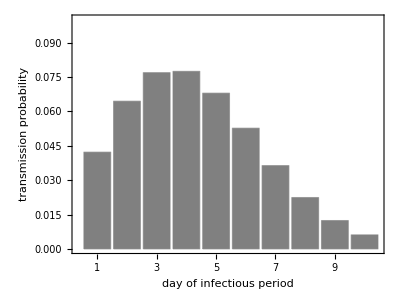

```mathematica
figure1a=Show[BarChart[probtransm[transmissibility],AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{All,{0.0,0.1}},ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}, FrameStyle->Directive[Black,17],FrameLabel->{"day of infectious period", "transmission probability"}](*,Graphics[Text[StyleForm["A",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,0.12*0.95}]]*)]
```

probability of developing symptoms by time since becoming infectious:

```mathematica
probsympdata={0.0209371,0.0461089,0.0813067,0.122817,0.165713,0.202934,0.224878,0.220575,0.183746,0.123545};
```

```mathematica
calcsymp[x_]=Total[Table[Product[(1-x*probsympdata[[j-1]]),{j,2,i}]*x*probsympdata[[i]],{i,1,infectious}]];
scenarioasymptomatic=Table[FindRoot[calcsymp[x]==1-0.05*(i-1),{x,0.5}],{i,1,20}][[All,1,2]];
```

```mathematica
factorasymptomatic=scenarioasymptomatic[[5]];
```

```mathematica
probsymp=factorasymptomatic*probsympdata
```

{0.0219031,0.0482363,0.0850581,0.128484,0.173359,0.212297,0.235254,0.230752,0.192224,0.129245}

```mathematica
probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];
```

```mathematica
fraccas=Total[probdevelopingsymptoms]
```

0.8

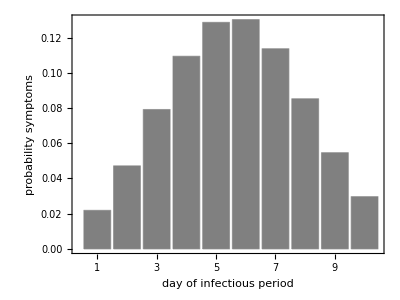

```mathematica
plotprobsymptoms=BarChart[probdevelopingsymptoms, Frame->True,ChartLabels->Table[i,{i,1,infectious}],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}, FrameStyle->Directive[Black,17], FrameLabel->{"day of infectious period", "probability symptoms"}]
```

distribution of the number of contacts with susceptibles by time since beginning of the infectious period:

```mathematica
saturation1=Drop[Prepend[Table[Product[1-probtransm[transmissibility][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.957803,0.89611,0.82724,0.763195,0.711364,0.673917,0.649437,0.634888,0.627034}

```mathematica
saturation2=Drop[Prepend[Table[Product[1-probtransm[transmissibility*transratio][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.989451,0.973518,0.954813,0.936333,0.920435,0.908322,0.900073,0.895033,0.892264}

```mathematica
BarChart[saturation1,ChartLabels->Table[i,{i,1,infectious}]];
```

```mathematica
mu1=meanhouseholdcontacts*saturation1*contactreduction1
```

{2.4,2.29873,2.15066,1.98537,1.83167,1.70727,1.6174,1.55865,1.52373,1.50488}

```mathematica
mu2=negbinn*saturation2*contactreduction2
```

{0.48,0.474936,0.467289,0.45831,0.44944,0.441809,0.435995,0.432035,0.429616,0.428287}

```mathematica
contactdist1=Array[f,infectious];contactdist2=Array[f,infectious];
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];
```

```mathematica
contact=Array[f,latent+infectious];
For [i=1,i≤infectious,i++,contact[[i]]=Mean[contactdist1[[i]]]+Mean[contactdist2[[i]]]]
```

```mathematica
numcontacts=Table[RandomVariate[contactdist1[[i]],1000]+RandomVariate[contactdist2[[i]],1000],{i,1,infectious}];
```

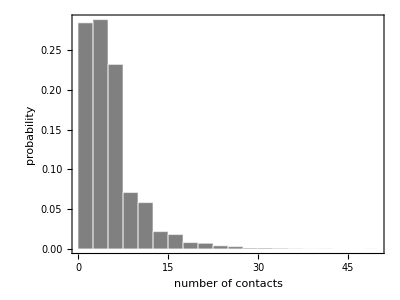

```mathematica
figure1b=Show[Histogram[RandomVariate[PoissonDistribution[meanhouseholdcontacts*contactreduction1],10000]+RandomVariate[NegativeBinomialDistribution[negbinn*contactreduction2,negbinp],10000], {0, 50, 2.5},"Probability", ChartBaseStyle->EdgeForm[White],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"number of contacts", "probability"},FrameTicks->{{True,None},{True,None}}](*,Graphics[Text[StyleForm["B",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(12.0-0.5)*0.1,0.17*0.95}]]*)]
```

```mathematica
Export[StringJoin["/Users/mirjam/Projects/Corona/LancetPHpaper/Figures/Figure_S2B_",date,".pdf"],figure1b,"pdf"];
```

```mathematica
meancontacts=Table[Mean[numcontacts[[i]]],{i,1,infectious}]//N
```

{5.009,4.788,4.807,4.433,4.427,4.292,4.081,3.822,3.953,3.905}

```mathematica
plotmeancontacts=BarChart[meancontacts, ChartLabels->Table[i,{i,1,infectious}],AxesLabel->{"day infectious period","mean number of contacts with susceptibles"}];
```

```mathematica
stdcontacts=Table[StandardDeviation[numcontacts[[i]]],{i,1,infectious}]//N
```

{4.12528,4.28456,4.47815,4.37294,4.29524,4.6954,4.1429,4.06286,4.16727,4.22822}

```mathematica
ListPlot[stdcontacts];
```

basic reproduction ratio:

```mathematica
rzero[pt_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])
```

```mathematica
Plot[rzero[x],{x,0,0.2},GridLines->{None,{2.5}}];
```

```mathematica
rzero1[pt_]:=∑_(i=1)^infectious Mean[contactdist1[[i]]]*probtransm[pt][[i]]
```

```mathematica
rzero2[pt_, tr_]:=∑_(i=1)^infectious Mean[contactdist2[[i]]]*probtransm[tr*pt][[i]]
```

```mathematica
rzero1[transmissibility]
```

0.904334

```mathematica
rzero2[transmissibility, transratio]
```

0.296756

```mathematica
rzero1[transmissibility]+rzero2[transmissibility,transratio]
```

1.20109

```mathematica
ratiohousehold[pt_, tr_]:=rzero1[pt]/(rzero1[pt]+rzero2[pt,tr]);
```

```mathematica
ratiohousehold[transmissibility, transratio]
```

0.752928

```mathematica
rzeroday[pt_]:=Table[Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[pt][[i]]*transratio, {i,1,infectious}]
```

```mathematica
rzeroperc=rzeroday[transmissibility]/rzero[transmissibility]*100
```

{10.8207,15.9357,17.9974,16.9823,13.9569,10.2258,6.75958,4.04869,2.19639,1.07649}

```mathematica
rzerocum=Table[∑_(i=1)^j rzeroperc[[i]], {j,1,infectious}];
```

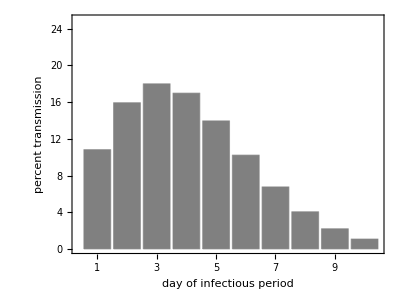

```mathematica
figure1c=Show[BarChart[rzeroperc,  AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],PlotRange->{All,{0,25}},Frame->True, FrameLabel->{"day of infectious period", "percent transmission"},FrameStyle->Directive[Black,17],  FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}](*,Graphics[Text[StyleForm["C",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,25*0.95}]]*)]
```

## Individual reproduction number

```mathematica
rzeroindiv[pt_]:= Sum[RandomVariate[BinomialDistribution[RandomVariate[contactdist1[[i]]],probtransm[pt][[i]]]]+RandomVariate[BinomialDistribution[RandomVariate[contactdist2[[i]]],probtransm[transratio*pt][[i]]]],{i,1,infectious}];
```

```mathematica
ListPlot[Table[{transmissibility*i,Around[Table[rzeroindiv[transmissibility*i],{k,1,100}]]},{i,1,3}],IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[Gray,Thickness[0.002]],Joined->True];
```

## Exponential growth rate and doubling time

```mathematica
startinf=Table[Product[(1-probinf[[k-1]]),{k,2,j}]*probinf[[j]],{j,1,latent}]
```

{0.5,0.35,0.15}

```mathematica
generations[r_,pt_]:=Sum[Sum[Exp[-r*(i+j)]*startinf[[j]](Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]),{i,1,infectious}],{j,1,latent}]
```

```mathematica
expgrowth[pt_]:=FindRoot[generations[r,pt]==1,{r,1}][[1,2]]
```

```mathematica
unconstrainedgrowth=expgrowth[transmissibility]
```

0.0325533

```mathematica
doublingtime[pt_]:=Log[2]/expgrowth[pt];
```

```mathematica
unconstraineddoubtime=doublingtime[transmissibility]
```

21.2927

## Definition of vaccination and quarantine parameters

```mathematica
timewindow=7;
```

probability of being diagnosed by day since first symptoms for the first index case:

```mathematica
probdiag:=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
probdiag[[1]]
```

{0.0175225,0.0385891,0.0680465,0.102787,0.138687,0.169838,0.188203,0.184602,0.153779,0.103396}

```mathematica
probbeingdiagnosed=Table[Table[Product[(1-probdiag[[ds,j-1]]),{j,2,i}]*probdiag[[ds,i]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
Total[Transpose[probbeingdiagnosed]][[1]]
```

0.716373

```mathematica
probdiagapp[fa_]=Table[Table[If[i<ds ,0.0,fa*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
cumprobbeingdiagnosed=Table[Table[Sum[probbeingdiagnosed[[j,k]],{k,1,i}],{i,1,infectious}],{j,1,infectious}];
```

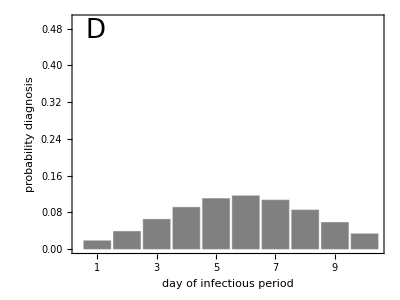

```mathematica
figure1d=Show[BarChart[probbeingdiagnosed[[1]], PlotRange->{All,{0,0.5}}, AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5], FrameStyle->Directive[Black,17],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["D",FontSize->26],{(10.0-0.5)*0.1,0.5*0.95}]]]
```

contact tracing and vaccination:

probability of being diagnosed on day i, if one has not been diagnosed up to day j (i>j):

```mathematica
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
sums=Table[∑_(k=1)^(infectious-j) pd[[1,j,k]],{j,1,infectious-1}]
```

{0.711315,0.699728,0.677803,0.640892,0.583069,0.497771,0.381337,0.241275,0.103396}

```mathematica
BarChart[sums, ChartStyle->{GrayLevel[0.8]},ChartLabels->Table[i,{i,1,infectious}],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{Automatic,Automatic,None,None}];
```

```mathematica
rzerodayprob=rzeroday[transmissibility]/rzero[transmissibility]
```

{0.108207,0.159357,0.179974,0.169823,0.139569,0.102258,0.0675958,0.0404869,0.0219639,0.0107649}

```mathematica
cumrzerodayprob=Table[Sum[rzerodayprob[[j]],{j,1,i}],{i,1,infectious}]
```

{0.108207,0.267564,0.447538,0.617361,0.756931,0.859189,0.926784,0.967271,0.989235,1.}

```mathematica
transmissionweights=PadRight[1-Total[Table[startinf[[k]]*PadLeft[Drop[cumrzerodayprob,-k],infectious],{k,1,latent}]],infectious+timewindow]
```

{1.,0.945897,0.828346,0.666352,0.494546,0.338327,0.212876,0.122352,0.0631115,0.0278198,0,0,0,0,0,0,0}

probability of a contact being isolated by day since first symptoms of source (probtrace2: source is secondary case, contact is ring 1; probtrace3: source is secondary case, contact is ring 2):

```mathematica
probtrace[vd_,cv_,fa_]:=fa*Table[Flatten[{Table[∑_(j=i)^Min[i-1+Length[pd[[ds,i]]],i+timewindow] pd[[ds,i,j-i+1]]*cv*transmissionweights[[j+vd-1]],{i,1,infectious-1}],0}],{ds,1,infectious}];
```

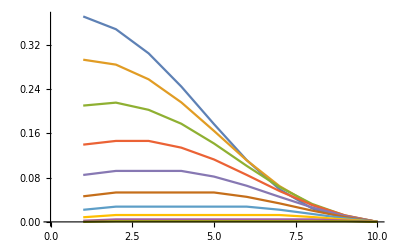

```mathematica
ListPlot[probtrace[1,1,1],Joined->True]
```

```mathematica
Mean[WeibullDistribution[3,7.2]]//N
```

6.42945

```mathematica
StandardDeviation[WeibullDistribution[3,7.2]]//N
```

2.33676

```mathematica
plotweibull=Plot[PDF[WeibullDistribution[3,7.2],x],{x,0,10}];
```

```mathematica
plotincubation=ListPlot[Total[Table[startinf[[k]]*PadLeft[Drop[probdevelopingsymptoms,-k],infectious],{k,1,latent}]],PlotMarkers->"OpenMarkers",PlotStyle->Red];
```

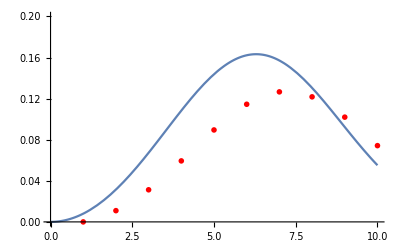

```mathematica
Show[plotweibull,plotincubation,PlotRange->{All,{0,0.2}}]
```

effective reproduction ratio with diagnosis probability  as above for all infecteds:

```mathematica
reffiso[pt_,ds_]:=∑_(i=1)^infectious ((Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

effective reproduction ratio with contact tracing:

```mathematica
reffvacc1[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc2[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious ( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probtrace[vd2,cv2,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=reffvacc1[pt,vd1,vd2,cv1,cv2,ds,fa]+reffvacc2[pt,vd1,vd2,cv1,cv2,ds,fa]
```

## Exponential growth rate and doubling time

```mathematica
generationseff[r_,pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious Sum[Exp[-r*(i+k)]*startinf[[k]]*((Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))+( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probtrace[vd2,cv2,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))),{k,1,latent}];
```

```mathematica
expgrowtheff[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=FindRoot[generationseff[r,pt,vd1,vd2,cv1,cv2,ds,fa]==1,{r,1}][[1,2]]
```

```mathematica
doublingtimeeff[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=Log[2]/expgrowtheff[pt,vd1,vd2,cv1,cv2,ds,fa];
```

## Specific parameter values

```mathematica
vaccdelay2=1.0;vaccdelay3=1.0;coverage2=0.8; coverage3=0.8;diagdelay=5;
```

```mathematica
colorscheme=Table[RGBColor[0,1-0.2*(k-1),1], {k,1,5}];
```

```mathematica
reffiso[transmissibility,diagdelay]
```

1.17894

```mathematica
reffvacc1[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

0.842936

```mathematica
reffvacc2[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

0.275968

```mathematica
reffvacc[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

1.1189

```mathematica
doubeff=doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

34.5918

```mathematica
doubincrease=doubeff/unconstraineddoubtime
```

1.62459

```mathematica
legend3=LineLegend[ Table[RGBColor[(k-1) 0.2,0.2( k-1),1],{k,{1,2,3,4}}],Table[j,{j,{0,1,2,3}}],LegendLabel->"D_2 (days)",LabelStyle->Directive[Black,14], LegendMargins->5]
```

```mathematica
labelgraph="Fraction symptomatic tested ";
```

```mathematica
yrange={0.7,1.3};
```

```mathematica
figure1= Show[Table[ListPlot[Table[{dd-1,reffvacc[transmissibility,k,k,coverage2,coverage3,dd,fractest]},{dd,1,8}],PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.2*(k-1),0.2*(k-1),1],Thickness[0.01]},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,{1,2,3,4}}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]],Graphics[Inset[legend3,{6.0,0.85}]]];
```

```mathematica
covvalues={3,5,7,9}
```

{3,5,7,9}

```mathematica
legend4=LineLegend[ Table[RGBColor[(k-1) 0.1,0.1( k-1),1],{k,covvalues}],Table[NumberForm[1*(1-(j-1)*0.1),{2,1}],{j,covvalues}],LegendLabel->"Tracing coverage",LabelStyle->Directive[Black,14], LegendMargins->5]
```

```mathematica
figure2= Show[Table[ListPlot[Table[{dd-1,reffvacc[transmissibility,vaccdelay2,vaccdelay3,fractionapp*(1-(k-1)*0.1),fractionapp*(1-(k-1)*0.1),dd,fractest]},{dd,1,8}],PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.1*(k-1),0.1*(k-1),1],Thickness[0.01]},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,covvalues}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]],Graphics[Inset[legend4,{6.0,0.85}]]];
```

```mathematica
figureisolation= Show[ListPlot[Table[{dd-1,reffvacc[transmissibility,vaccdelay2,vaccdelay3,0,0,dd,fractest]},{dd,1,8}],PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.0,0.4,0.0],Thickness[0.01]},LabelStyle->{RGBColor[0,0.4,0],14},PlotLabels->Placed["isolation",{Scaled[0.12],Top}],GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,None}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]]];
```

```mathematica
figurecoverage=Show[figure2,figureisolation,FrameTicks->{{Automatic,None},{Automatic,None}}];
```

```mathematica
figuretracingdelay=Show[figure1,figureisolation,FrameTicks->{Automatic, Automatic, None, None}];
```

```mathematica
legend1=LineLegend[{RGBColor[1, 0.49, 0], RGBColor[0,0.6,1], RGBColor[0,0.4,1]},{ "Conventional CT","Mobile App CT 80%", "Mobile App CT 60%"},LegendLabel->"CTS",LabelStyle->Directive[GrayLevel[0],14],LegendMargins->5]
```

```mathematica
figure4= Show[ListPlot[{Table[{dd-1,reffvacc[transmissibility,1,1,0.8,0.8,dd,0.8]},{dd,1,8}],Table[{dd-1,reffvacc[transmissibility,1,1,0.6,0.6,dd,0.6]},{dd,1,8}],Table[{dd-1,reffvacc[transmissibility,4,4,0.8,0.5,dd,fractest]},{dd,1,10}]},PlotRange->{All,{0.6,1.3}},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{{RGBColor[0.0,0.4,1],Thickness[0.01]},{RGBColor[0,0.6,1],Thickness[0.01]},{RGBColor[1,0.5,0.0],Thickness[0.01]}},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,ct]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractionapp*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]],Graphics[Inset[legend1,{5.0,0.85}]]];
```

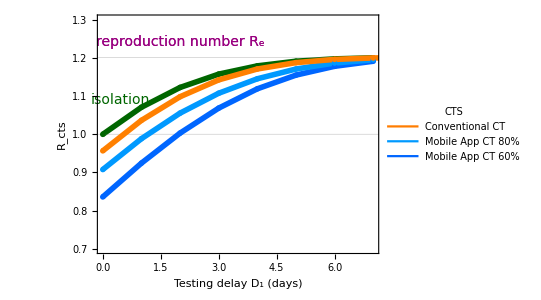

```mathematica
figure3apaper=Show[figureisolation,figure4,PlotRange->{{0,7},{0.7,1.3}},FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Table[{dd-1,reffvacc[transmissibility,1,1,1,1,dd,0.8]},{dd,1,8}]
```

{{0,0.79507},{1,0.887847},{2,0.973144},{3,1.04616},{4,1.1039},{5,1.14565},{6,1.17295},{7,1.18883}}

```mathematica
Table[{dd-1,reffvacc[transmissibility,1,1,0.8,0.8,dd,0.8]},{dd,1,8}]
```

{{0,0.836016},{1,0.924398},{2,1.003},{3,1.06839},{4,1.1189},{5,1.15474},{6,1.1778},{7,1.19105}}

```mathematica
xvalues=Table[rzero[x],{x,0.05,0.1,0.01}];
```

```mathematica
yvalues1=Table[reffiso[x,1],{x,0.05,0.1,0.01}];
```

```mathematica
yvalues2=Table[reffvacc[x,1,1,1.0,1.0,1],{x,0.05,0.1,0.01}];
```

```mathematica
prevapp=0.6;
```

```mathematica
reffcombined=(1-prevapp)*reffvacc[transmissibility,4,4,0.8,0.5,5,fractest]+prevapp*reffvacc[transmissibility,1,1,prevapp,prevapp,1,1.0]
```

0.976052

```mathematica
labelspercent1={ToString[NumberForm[100.0,{3,1}]],ToString[NumberForm[reffiso[transmissibility,5]/rzero[transmissibility]*100,{3,1}]],ToString[NumberForm[reffvacc[transmissibility,4,4,0.8,0.5,5,fractest]/rzero[transmissibility]*100,{3,1}]],ToString[NumberForm[reffvacc[transmissibility,1,1,0.6,0.6,1,0.6]/rzero[transmissibility]*100,{3,1}]],ToString[NumberForm[reffvacc[transmissibility,1,1,0.8,0.8,1,0.8]/rzero[transmissibility]*100,{3,1}]],ToString[NumberForm[reffvacc[transmissibility,1,1,1.0,1.0,1,1.0]/rzero[transmissibility]*100,{3,1}]]}
```

{100.0,98.2,97.5,75.6,69.6,61.9}

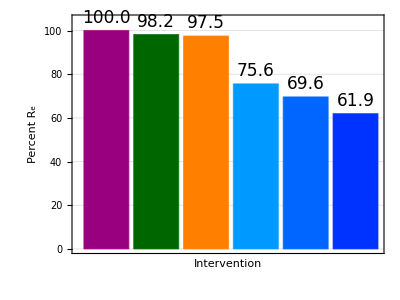

```mathematica
figure5=BarChart[{100,reffiso[transmissibility,5]/rzero[transmissibility]*100,reffvacc[transmissibility,4,4,0.8,0.5,5,fractest]/rzero[transmissibility]*100,reffvacc[transmissibility,1,1,0.6,0.6,1,0.6]/rzero[transmissibility]*100,reffvacc[transmissibility,1,1,0.8,0.8,1,0.8]/rzero[transmissibility]*100,reffvacc[transmissibility,1,1,1.0,1.0,1,1.0]/rzero[transmissibility]*100},PlotRange->{All,{0,105}},ChartLabels->Placed[labelspercent1,Above],  GridLines->{None,Automatic},ChartStyle->{RGBColor[3* 0.2,0.0,0.5],RGBColor[0,0.4,0],RGBColor[1,0.5,0.0],RGBColor[0,0.6,1],RGBColor[0,0.4,1],RGBColor[0.0,0.2,1]}, LabelStyle->Directive[Black,17],(*ChartLegends->SwatchLegend[{"Social distancing","Isolation","Conventional CT","Tracing app CT 60%","Tracing app CT 80%","Tracing app CT 100%"},LegendMarkerSize->20,LabelStyle->Directive[Black,17]],*)Frame->True,FrameStyle->{{Directive[Black,17],None},{Directive[Black,17],None}}, FrameTicks->{{Automatic, None},{Automatic, None}},FrameLabel->{"Intervention","Percent R_e"},AspectRatio->AspRat,ImageSize->ImSize]
```

```mathematica
labelspercent2= Table[ToString[NumberForm[reffvacc[transmissibility,1,1,k*0.2,k*0.2,1,k*0.2]/rzero[transmissibility]*100,{3,1}]],{k,1,5}]
```

{82.4,79.8,75.6,69.6,61.9}

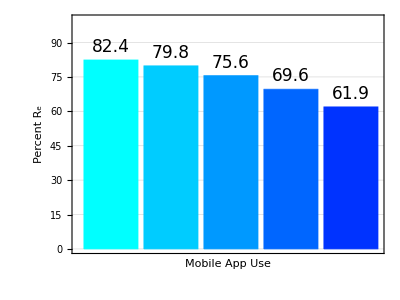

```mathematica
figure6=BarChart[Table[reffvacc[transmissibility,1,1,k*0.2,k*0.2,1,k*0.2]/rzero[transmissibility]*100,{k,1,5}],PlotRange->{All,{0,100}},GridLines->{None,Automatic},ChartStyle->colorscheme, (*ChartLegends->SwatchLegend[{Table[StringJoin[ToString[NumberForm[(k*0.2)*100,{3,1}]],"%"],{k,1,5}]},LegendMarkerSize->20,LabelStyle->Directive[Black,17]],*)ChartLabels->Placed[labelspercent2,Above],LabelStyle->Directive[Black,17],Frame->True,FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},FrameLabel->{"Mobile App Use","Percent R_e"},AspectRatio->AspRat,ImageSize->ImSize]
```

```mathematica
result={};
Do[probdiag=probdiagapp[k*0.2];result=Append[result,reffvacc[transmissibility,1,1,k*0.2,k*0.2,1,k*0.2]/rzero[transmissibility]*100],{k,1,5}]
```

```mathematica
result
```

{94.3146,87.3057,79.0465,69.6048,59.0435}

```mathematica
labelspercent3= Table[ToString[NumberForm[result[[k]],{3,1}]],{k,1,5}]
```

{94.3,87.3,79.0,69.6,59.0}

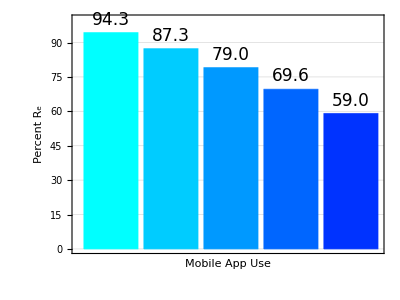

```mathematica
figure7=BarChart[result,PlotRange->{All,{0,100}},GridLines->{None,Automatic},ChartStyle->colorscheme, (*ChartLegends->SwatchLegend[{Table[StringJoin[ToString[NumberForm[(k*0.2)*100,{3,1}]],"%"],{k,1,5}]},LegendMarkerSize->20,LabelStyle->Directive[Black,17]],*)ChartLabels->Placed[labelspercent3,Above],LabelStyle->Directive[Black,17],Frame->True,FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},FrameLabel->{"Mobile App Use","Percent R_e"},AspectRatio->AspRat,ImageSize->ImSize]
```

## Individual effective reproduction numbers

```mathematica
reffisoindiv[pt_,ds_]:= Total[Table[(RandomVariate[BinomialDistribution[RandomVariate[contactdist1[[i]]],probtransm[pt][[i]]]]+RandomVariate[BinomialDistribution[RandomVariate[contactdist2[[i]]],probtransm[transratio*pt][[i]]]]),{i,1,infectious}]*Table[Product[1-RandomVariate[BernoulliDistribution[probdiag[[ds,j]]]],{j,1,i-1}],{i,1,infectious}]];
```

```mathematica
refftraceindiv1[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=Total[Table[RandomVariate[BinomialDistribution[RandomVariate[contactdist1[[i]]],probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])]],{i,1,infectious}]*Table[ Product[1-RandomVariate[BernoulliDistribution[probdiag[[ds,j]]]],{j,1,i-1}],{i,1,infectious}]]
```

```mathematica
refftraceindiv2[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=Total[Table[RandomVariate[BinomialDistribution[RandomVariate[contactdist2[[i]]],probtransm[transratio*pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])]],{i,1,infectious}]*Table[ Product[1-RandomVariate[BernoulliDistribution[probdiag[[ds,j]]]],{j,1,i-1}],{i,1,infectious}]]
```

```mathematica
refftraceindiv[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=refftraceindiv1[pt,vd1,vd2,cv1,cv2,ds,fa]+refftraceindiv2[pt,vd1,vd2,cv1,cv2,ds,fa]
```

```mathematica
reffisoindiv[transmissibility,1]
```

0

```mathematica
refftraceindiv[transmissibility,1,1,1,1,3,0.8]
```

2

```mathematica
simdatarzero=Table[rzeroindiv[transmissibility],{k,1,1000}];
```

```mathematica
simdatariso=Table[Table[reffisoindiv[transmissibility,j],{k,1,1000}],{j,1,8}];
```

$Aborted

```mathematica
simdatareff1=Table[Table[refftraceindiv[transmissibility,1,1,1,1,j,1],{k,1,1000}],{j,1,8}];
```

```mathematica
simdatarefftracingdelay=Table[Table[Table[refftraceindiv[transmissibility,d2,d2,0.8,0.8,j,fractest],{k,1,1000}],{j,1,8}],{d2,1,4}];
```

```mathematica
simdatarefftracingcoverage=Table[Table[Table[refftraceindiv[transmissibility,1,1,1-0.2(cv-1),1-0.2(cv-1),j,fractest],{k,1,1000}],{j,1,8}],{cv,1,4}];
```

```mathematica
plotboxplotsreff=BoxWhiskerChart[{simdatarzero,simdatariso[[5]],simdatareff1[[1]]},{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},ChartStyle->{RGBColor[3* 0.2,0.0,0.5],RGBColor[0,0.4,0],RGBColor[0.0,0.0,1],RGBColor[0,0.8,1],RGBColor[1,0.5,0.0]},ChartLabels->{"R_e","R_iso","R_cts"},AspectRatio->AspRat,ImageSize->ImSize,FrameStyle->Directive[Black,17], FrameTicks->{{Automatic, None},{ Automatic, None}},GridLines->{None,{1}}];
```

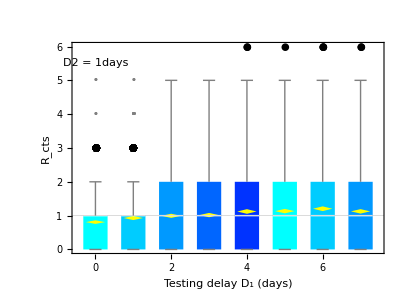
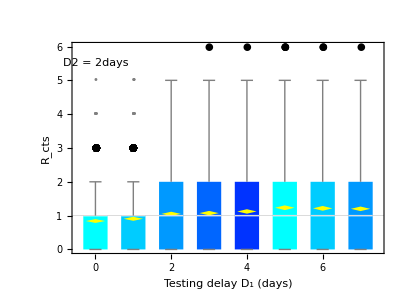
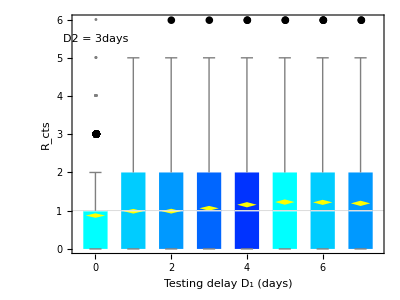
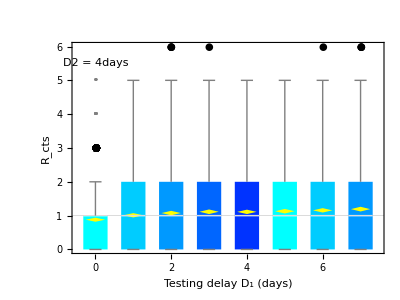

```mathematica
plotboxplotsrefftracingdelay=Table[Show[BoxWhiskerChart[simdatarefftracingdelay[[k,All]],{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},ChartStyle->colorscheme,ChartLabels->Table[i-1,{i,1,8}],PlotRange->{All,{0,6}},AspectRatio->AspRat,ImageSize->ImSize,FrameStyle->Directive[Black,17], FrameTicks->{{Automatic, None},{ Automatic, None}},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,None}},GridLines->{None,{1}}],Graphics[Inset[StringJoin["D2 = ",ToString[k],"days"],{1,5.5}]]],{k,1,4}]
```

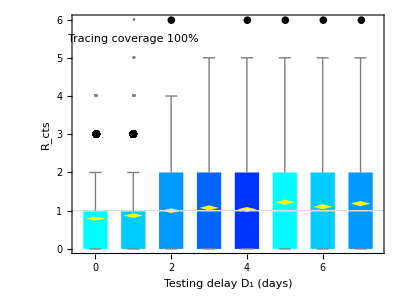
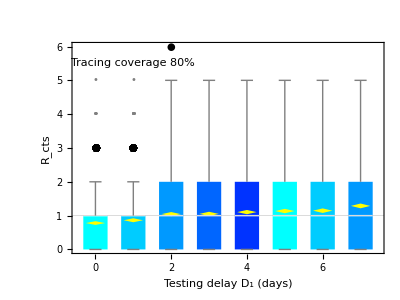
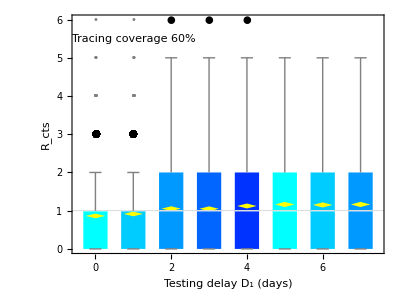
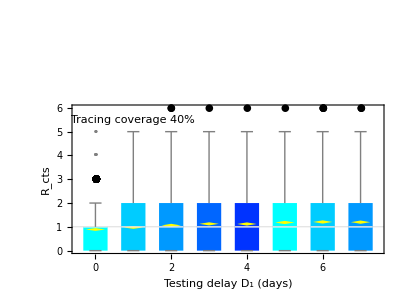

```mathematica
plotboxplotsrefftracingcoverage=Table[Show[BoxWhiskerChart[simdatarefftracingcoverage[[cv,All]],{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},ChartStyle->colorscheme,ChartLabels->Table[i-1,{i,1,8}],PlotRange->{All,{0,6}},AspectRatio->AspRat,ImageSize->ImSize,FrameStyle->Directive[Black,17], FrameTicks->{{Automatic, None},{ Automatic, None}},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,None}},GridLines->{None,{1}}],Graphics[Inset[StringJoin["Tracing coverage ",ToString[IntegerPart[(1-0.2*(cv-1))*100+0.001]],"%"],{2,5.5}]]],{cv,1,4}]
```

```mathematica
ListPlot[Table[Around[simdatarzero],{j,0,8}],Joined->True,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[Gray,Thickness[0.002]], PlotRange->{All,{0,4}}];
```

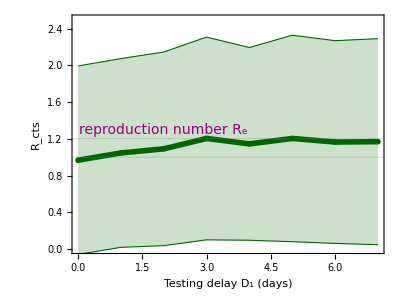

```mathematica
figure3uncertainty=Show[ListPlot[Table[{j-1,Around[simdatariso[[j]]]},{j,1,8}],IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[RGBColor[0.0,0.4,0.0],Thickness[0.002]],Joined->True,PlotRange->{All,{0,2.5}},PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.0,0.4,0.0],Thickness[0.01]},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,None}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.1}]]]
```

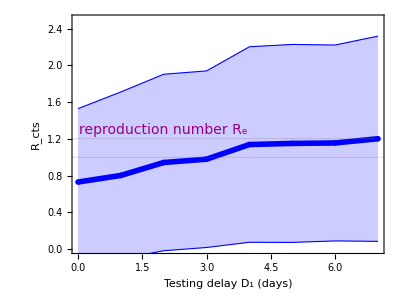

```mathematica
figure2uncertainty=Show[ListPlot[Table[{j-1,Around[simdatareff1[[j]]]},{j,1,8}],IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[RGBColor[0,0,1],Thickness[0.002]],Joined->True,PlotRange->{All,{0,2.5}},PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0,0,1],Thickness[0.01]},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.1}]]]
```

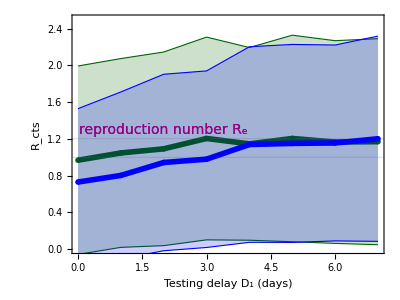

```mathematica
figureuncertainty=Show[figure3uncertainty,figure2uncertainty]
```

```mathematica
simdatareffconventionalCT=Table[refftraceindiv[transmissibility,4,4,0.8,0.5,5,fractest],{k,1,1000}];
```

```mathematica
simdatareffmobileapp=Table[refftraceindiv[transmissibility,1,1,fractionapp,fractionapp,1,fractionapp],{k,1,1000}];
```

```mathematica
plotboxplotscompint=BoxWhiskerChart[{simdatarzero,simdatariso[[5]],simdatareffconventionalCT,simdatareffmobileapp},{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},ChartStyle->colorscheme,AspectRatio->AspRat,ImageSize->ImSize,FrameStyle->Directive[Black,17], ChartLegends->{"Physical distancing","Isolation","Conventional CT","Tracing app CT"},FrameTicks->{{Automatic, None},{ Automatic, None}},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Intervention",None}},GridLines->{None,{1}}];
```

```mathematica
simdatareffmobileappfraction=Table[Table[refftraceindiv[transmissibility,1,1,j*0.2,j*0.2,1,j*0.2],{k,1,1000}],{j,1,5}];
```

```mathematica
colorscheme=Table[RGBColor[0,1-0.2*(k-1),1], {k,1,5}];
```

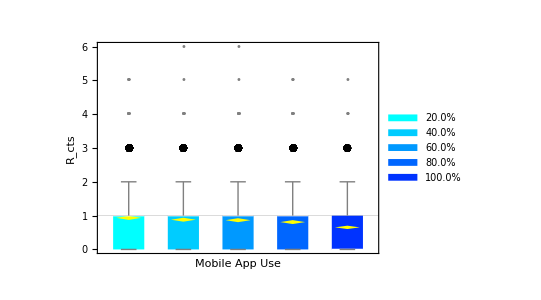

```mathematica
plotboxplotsfracmobapp=BoxWhiskerChart[simdatareffmobileappfraction,{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},ChartStyle->colorscheme,AspectRatio->AspRat,ImageSize->ImSize,FrameStyle->Directive[Black,17], PlotRange->{All,{0,6}},ChartLegends->SwatchLegend[{Table[StringJoin[ToString[NumberForm[(k*0.2)*100,{3,1}]],"%"],{k,1,5}]},LegendMarkerSize->20,LabelStyle->Directive[Black,17]],FrameTicks->{{Automatic, None},{ Automatic, None}},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Mobile App Use",None}},GridLines->{None,{1}}]
```

```mathematica
result2={};
Do[probdiag=probdiagapp[j*0.2];result2=Append[result2,Table[refftraceindiv[transmissibility,1,1,j*0.2,j*0.2,1,j*0.2],{k,1,1000}]],{j,1,5}]
```

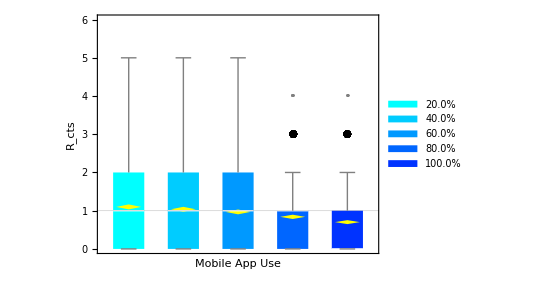

```mathematica
plotboxplotsfracmobapp2=BoxWhiskerChart[result2,{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},ChartStyle->colorscheme,AspectRatio->AspRat,PlotRange->{All,{0,6}},ImageSize->ImSize,FrameStyle->Directive[Black,17], ChartLegends->SwatchLegend[{Table[StringJoin[ToString[NumberForm[(k*0.2)*100,{3,1}]],"%"],{k,1,5}]},LegendMarkerSize->20,LabelStyle->Directive[Black,17]],FrameTicks->{{Automatic, None},{ Automatic, None}},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Mobile App Use",None}},GridLines->{None,{1}}]
```

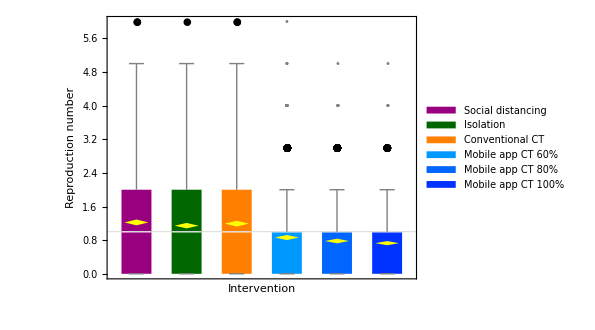

```mathematica
plotboxplotsreff2=BoxWhiskerChart[{simdatarzero,simdatariso[[5]],simdatareffconventionalCT,simdatarefftracingcoverage[[3,1]],simdatarefftracingcoverage[[2,1]], simdatareff1[[1]]},{"Outliers",{"MeanDiamond",0.8,Yellow},{"Outliers", Black}},PlotRange->{All,{0,6}},ChartStyle->{RGBColor[3* 0.2,0.0,0.5],RGBColor[0,0.4,0],RGBColor[1,0.5,0.0],RGBColor[0,0.6,1],RGBColor[0,0.4,1],RGBColor[0.0,0.2,1]},ChartLegends->SwatchLegend[{"Physical distancing","Isolation","Conventional CT","Mobile app CT 60%", "Mobile app CT 80%","Mobile app CT 100%"},LegendMarkerSize->20,LabelStyle->Directive[Black,17]],AspectRatio->AspRat,ImageSize->ImSize*1.1,FrameStyle->Directive[Black,17], FrameTicks->{{Automatic, None},{ Automatic, None}},GridLines->{None,{1}},FrameLabel->{{ "Reproduction number",None},{"Intervention",None}}]
```

## Varying fraction testing

```mathematica
fractest=0.8; diagdelay=5;simdatarisotest={};simdatactconventionaltest={};simdatareffmobileapptest={};
```

```mathematica
Do[fractest=0.2*i;
probdiag=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
simdatarisotest=Append[simdatarisotest,Table[reffisoindiv[transmissibility,diagdelay],{k,1,1000}]];
simdatactconventionaltest=Append[simdatactconventionaltest,Table[refftraceindiv[transmissibility,4,4,0.8,0.5,diagdelay,fractest],{k,1,1000}]];,{i,1,5}]
```

```mathematica
testlabel=Table[ToString[IntegerPart[i *0.2*100]],{i,1,5}]
```

{20,40,60,80,100}

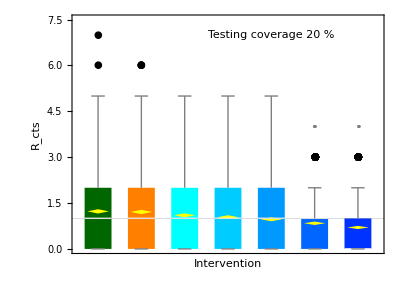
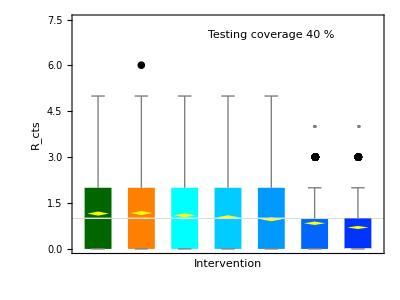
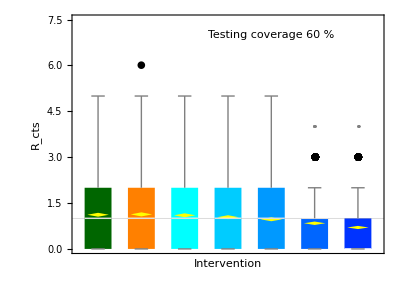
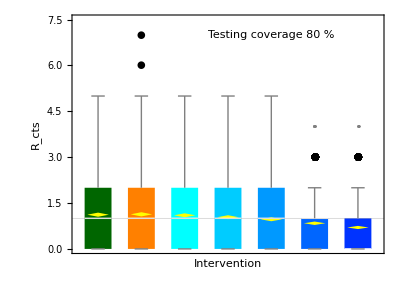

```mathematica
plotboxplotstesting=Table[Show[BoxWhiskerChart[{simdatarisotest[[i]],simdatactconventionaltest[[i]],result2[[1]],result2[[2]],result2[[3]],result2[[4]],result2[[5]]},{"Outliers", {"MeanDiamond",0.8,Yellow},{"Outliers", Black}},PlotRange->{All,{0,7.5}},ChartStyle->{RGBColor[0,0.4,0],RGBColor[1,0.5,0.0],RGBColor[0,1,1],RGBColor[0,0.8,1],RGBColor[0,0.6,1],RGBColor[0,0.4,1],RGBColor[0.0,0.2,1]},AspectRatio->AspRat,ImageSize->ImSize,FrameStyle->Directive[Black,17], (*ChartLegends->Placed[{"Isolation","Conventional CTS","20% Mobile App Use","40% Mobile App Use","60% Mobile App Use","80% Mobile App Use","100% Mobile App Use"},Bottom],*)FrameTicks->{{Automatic, None},{ Automatic, None}},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Intervention",None}},GridLines->{None,{1}}],Graphics[Inset[StringJoin["Testing coverage ",testlabel[[i]]," %"],{5,7.0}]]],{i,1,4}]
```

```mathematica
figure7legend=SwatchLegend[{RGBColor[0,0.4,0],RGBColor[1,0.5,0.0],RGBColor[0,1,1],RGBColor[0,0.8,1],RGBColor[0,0.6,1],RGBColor[0,0.4,1],RGBColor[0.0,0.2,1]},{"Isolation","Conventional CTS","20% Mobile App Use","40% Mobile App Use","60% Mobile App Use","80% Mobile App Use","100% Mobile App Use"},LegendMarkerSize->20,LabelStyle->Directive[Black,17],LegendLayout->"Column"]
```

## Transmission prevented per diagnosed case

```mathematica
factorasymptomatic=scenarioasymptomatic[[1]]
```

4.44686

```mathematica
fractest=1.0;
```

```mathematica
probsymp=factorasymptomatic*probsympdata;
```

```mathematica
probdiag=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
preventedisolation=Table[(rzero[transmissibility]-reffiso[transmissibility,ds])/rzero[transmissibility]*100,{ds,1,infectious-3}]
```

{50.4216,35.725,23.4297,14.1506,7.77839,3.79619,1.57086}

```mathematica
preventedct=Table[Table[(rzero[transmissibility]-(reffvacc1[transmissibility,vd,vd,0.8,0.8,ds,1.0]+reffvacc2[transmissibility,vd,vd,0.8,0.8,ds,1.0]))/rzero[transmissibility]*100,{ds,1,infectious-3}],{vd,1,5}];
```

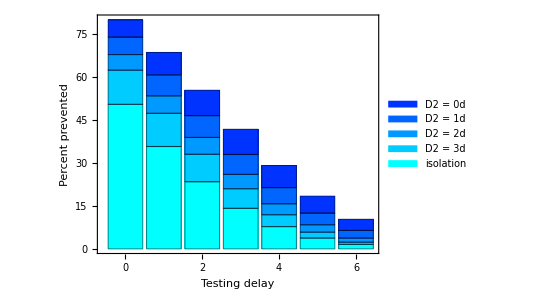

```mathematica
plottransmissionprevented=BarChart[Transpose[{preventedisolation,preventedct[[4]]-preventedisolation,preventedct[[3]]-preventedct[[4]],preventedct[[2]]-preventedct[[3]],preventedct[[1]]-preventedct[[2]]}],ChartLayout->"Stacked",PlotRange->{All,{0,80}}, AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->colorscheme,  ChartLegends->{"isolation","D2 = 3d","D2 = 2d","D2 = 1d", "D2 = 0d"},FrameStyle->Directive[Black,17],Frame->True, FrameLabel->{"Testing delay", "Percent prevented"},FrameTicks->{{True,None},{Table[{i,i-1},{i,1,infectious-3}],None}}]
```

```mathematica
tablefigure5=NumberForm[TableForm[Transpose[{preventedisolation,preventedct[[4]],preventedct[[3]],preventedct[[2]],preventedct[[1]]}]],{3,1}]
```

50.4 | 62.4 | 67.8 | 73.9 | 79.9
35.7 | 47.3 | 53.4 | 60.7 | 68.5
23.4 | 33.0 | 38.9 | 46.5 | 55.4
14.2 | 21.0 | 26.0 | 32.9 | 41.8
7.8 | 11.9 | 15.7 | 21.4 | 29.1
3.8 | 5.9 | 8.4 | 12.5 | 18.4
1.6 | 2.4 | 3.8 | 6.4 | 10.4

```mathematica
Export[StringJoin["/Users/mirjam/Projects/Corona/LancetPHpaper/Figures/Table3_",date,".txt"],tablefigure5,"Table"];
```

## Output

```mathematica
figurepaper2det=Show[figure3apaper, FrameTicks->{Automatic, Automatic, None, None}]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure2det_",date,".pdf"],figurepaper2det,"pdf"];
```

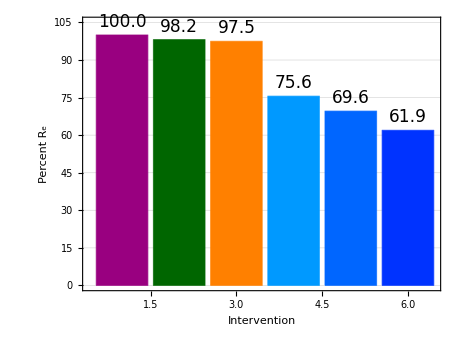

```mathematica
figurepaper3a=Show[figure5, ImageSize->1.15ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"Figure3a_",date,".pdf"],figurepaper3a,"pdf"];
```

```mathematica
figurepaper3b=Show[plotboxplotsreff2]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure3b_",date,".pdf"],figurepaper3b,"pdf"];
```

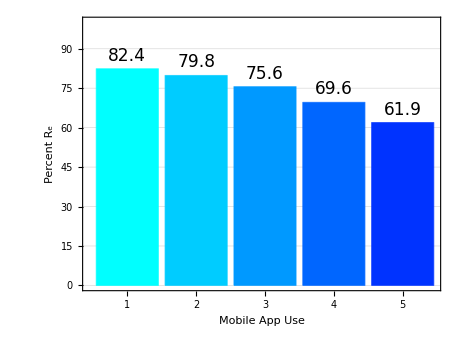

```mathematica
figurepaper4a=Show[figure6,ImageSize->1.15ImSize, FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"Figure4a_",date,".pdf"],figurepaper4a,"pdf"];
```

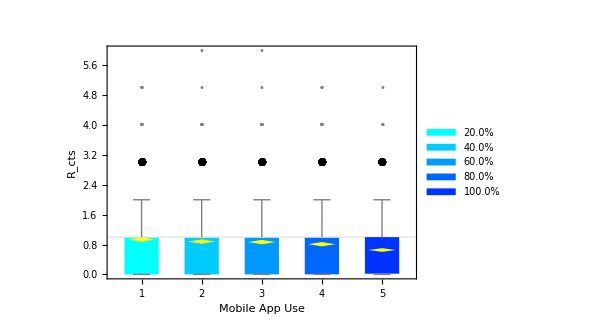

```mathematica
figurepaper4b=Show[plotboxplotsfracmobapp,  ImageSize->1.1ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"Figure4b_",date,".pdf"],figurepaper4b,"pdf"];
```

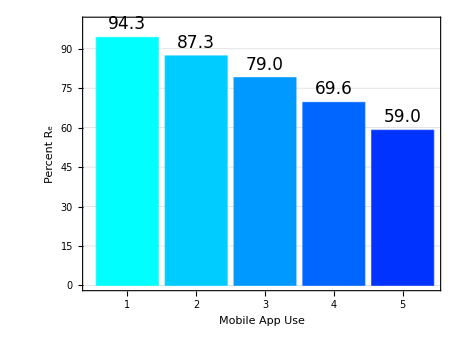

```mathematica
figurepaper4c=Show[figure7, ImageSize->1.15*ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"Figure4c_",date,".pdf"],figurepaper4c,"pdf"];
```

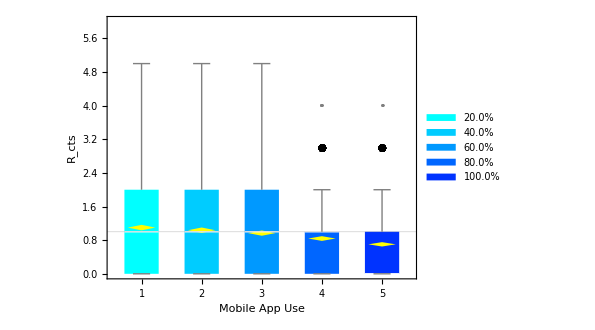

```mathematica
figurepaper4d=Show[ plotboxplotsfracmobapp2,ImageSize->1.1ImSize, FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"Figure4d_",date,".pdf"],figurepaper4d,"pdf"];
```

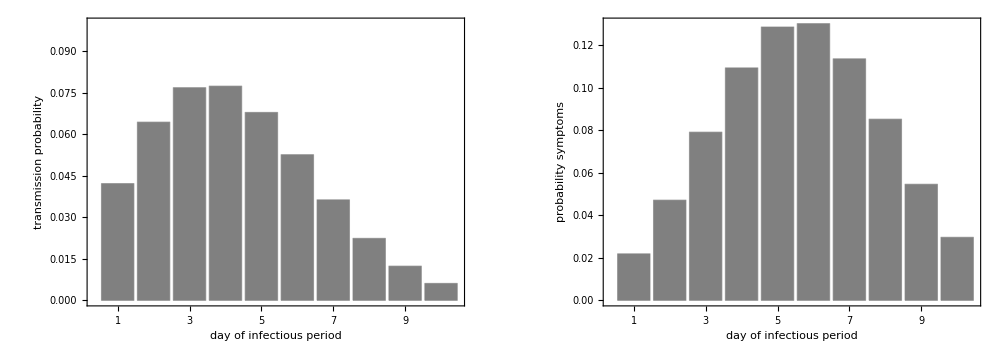

```mathematica
figureS1=Show[GraphicsRow[{figure1a,plotprobsymptoms}],GraphicsSpacing->0.01,ImageSize->2.5*ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"Figure_S1_",date,".pdf"],figureS1,"pdf"];
```

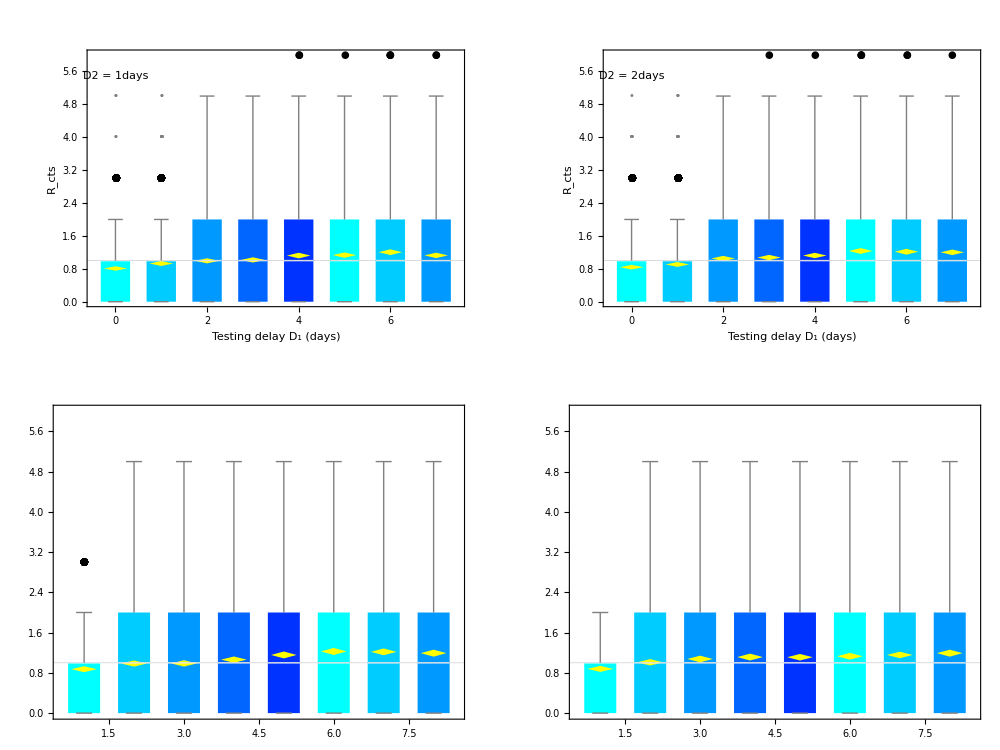

```mathematica
figurepaperS5=Show[GraphicsGrid[{{plotboxplotsrefftracingdelay[[1]],plotboxplotsrefftracingdelay[[2]]},{plotboxplotsrefftracingdelay[[3]],plotboxplotsrefftracingdelay[[4]]}}], GraphicsSpacing->0.01,ImageSize->2.5*ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"FigureS5_",date,".pdf"],figurepaperS5,"pdf"];
```

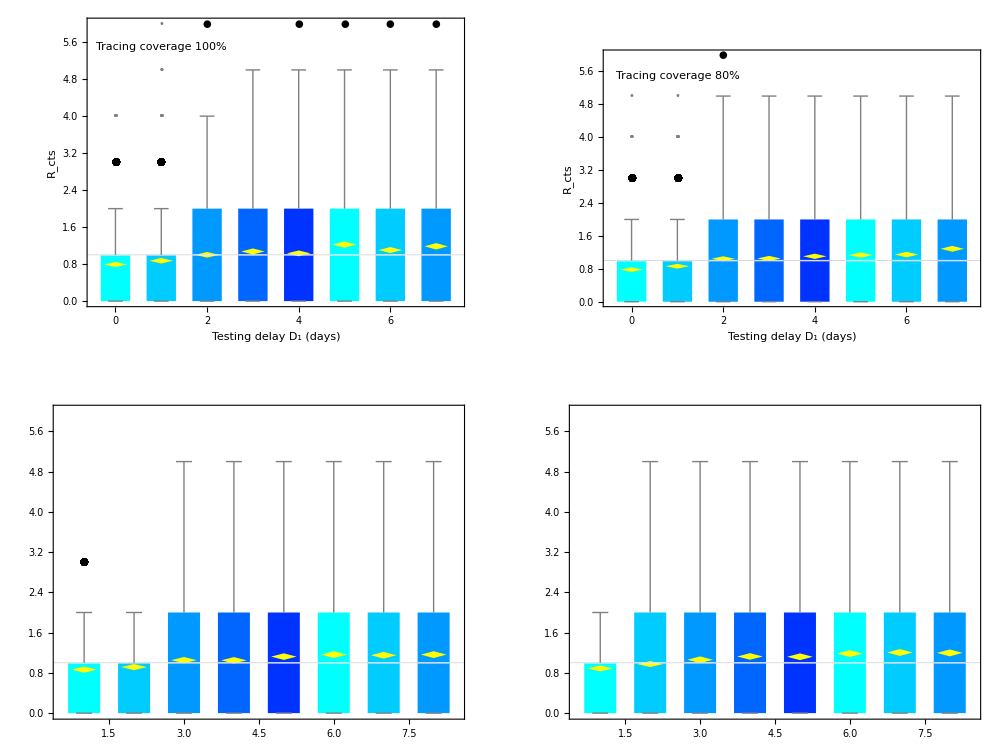

```mathematica
figurepaperS6=Show[GraphicsGrid[{{plotboxplotsrefftracingcoverage[[1]],plotboxplotsrefftracingcoverage[[2]]},{plotboxplotsrefftracingcoverage[[3]],plotboxplotsrefftracingcoverage[[4]]}}], GraphicsSpacing->0.01,ImageSize->2.5*ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"FigureS6_",date,".pdf"],figurepaperS6,"pdf"];
```

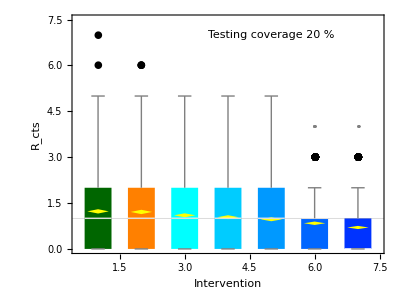

```mathematica
figureS7a=Show[plotboxplotstesting[[1]]  ,FrameTicks->{Automatic, Automatic, None, None} ]
```

```mathematica
Export[StringJoin[ filepath,"Figure_S7a_",date,".pdf"],figureS7a,"pdf"];
```

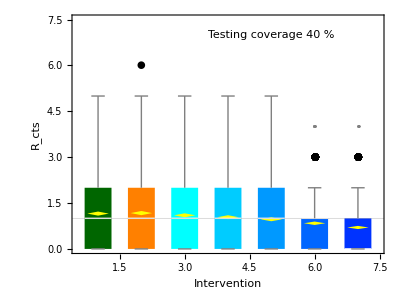

```mathematica
figureS7b=Show[plotboxplotstesting[[2]]  ,FrameTicks->{Automatic, Automatic, None, None} ]
```

```mathematica
Export[StringJoin[ filepath,"Figure_S7b_",date,".pdf"],figureS7b,"pdf"];
```

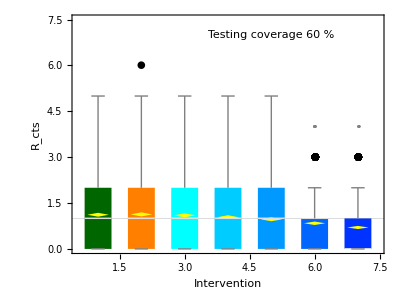

```mathematica
figureS7c=Show[plotboxplotstesting[[3]] ,FrameTicks->{Automatic, Automatic, None, None} ]
```

```mathematica
Export[StringJoin[ filepath,"Figure_S7c_",date,".pdf"],figureS7c,"pdf"];
```

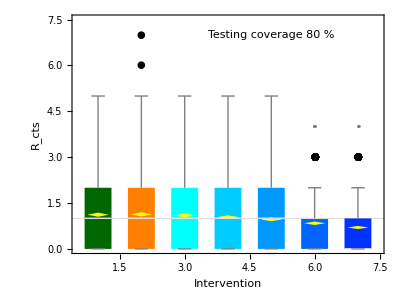

```mathematica
figureS7d=Show[plotboxplotstesting[[4]]  ,FrameTicks->{Automatic, Automatic, None, None} ]
```

```mathematica
Export[StringJoin[ filepath,"Figure_S7d_",date,".pdf"],figureS7d,"pdf"];
```

```mathematica
figure7legend
```

```mathematica
Export[StringJoin[ filepath,"Figure_S7legend_",date,".pdf"],figure7legend,"pdf"];
```